```mathematica
data:={{0,4.88},{4.7,6.92},{9.5,8.99},{14.3,11.09},{19.1,13.18},{23.9,15.26},{28.7,17.39},{0,4.95},{4.7,7.00},{9.5,9.10},{14.3,11.20},{19.1,13.30},{24.0,15.41},{28.7,17.51}}
```

```mathematica
n:=Length[data]
```

```mathematica
model=LinearModelFit[data,x,x]
```

FittedModel[4.90738+0.436293 x]

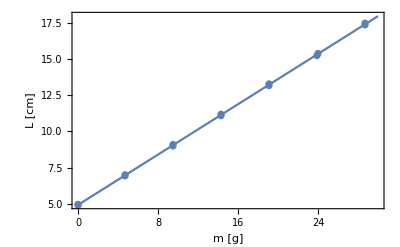

```mathematica
Show[Plot[model["BestFit"],{x,0,30},Frame->{True,True,False,False},FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{"m [g]","L [cm]"}],ListPlot[data]]
```

```mathematica
R2 =model["RSquared"]
```

0.999837

```mathematica
model["ParameterTable"]
```

```mathematica
{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {1, 4.907378740505933, 0.0276904, 177.22338178911846, 7.002014018081375*^-22}, {x, 0.4362927562739, 0.0016067826077910906, 271.5319136256332, 4.189432081964047*^-24}}
```

```mathematica
Syy=∑_(i=1)^n (data[[i]][[2]])^2-1/n(∑_(i=1)^n data[[i]][[2]])^2
```

244.912

```mathematica
Sxy=∑_(i=1)^n (data[[i]][[1]]*data[[i]][[2]])-1/n(∑_(i=1)^n data[[i]][[1]])(∑_(i=1)^n data[[i]][[2]])
```

561.257

```mathematica
SSE=Syy-model["BestFitParameters"][[2]]*Sxy
```

0.0398547

```mathematica
SSEpe=∑_(i=1)^(n/2) ∑_(j=1)^2 (data[[i+(j-1)*n/2]][[2]])^2-∑_(i=1)^(n/2) 1/2(∑_(j=1)^2 data[[i+(j-1)*n/2]][[2]])^2
```

0.0434